### Initializing

```mathematica
(*General program to get several values of energies for odd and even cases.*)
(*The numerical evaluation*)
Eval={};E0=0.5;dE=0.2;(*Initializing our Energy and its step to be as small as possible*)
xm=2.000;dx=0.01;xL=Chop[Range[-xm,xm,dx]];Lx=Length[xL]; (*Constructing the discritized x matrix*)
Vin=0;Vout=10^8;max=2;V=0*xL;Do[If[xL[[i]]<=-1||xL[[i]]>=1,V[[i]]=Vout],{i,Lx}]; (*Constructing V matrix*)
pos0=Position[xL,0][[1,1]]; (*Getting the position of x=0 in the position list because we just need to evaluate ψ from x=0 to x=xmax after exploiting the even and odd condition.*)
```

### Calculations

```mathematica
(*Here we go ...*)
(*1. First we reinitialize, then we check the eveness and oddness of the solution from the state number of are looking for.*)
(*2. After checking, we initialize the wavefunction at the origin to exploit the eveness and oddness.*)
(*3. The first while loop gives the initial wavefunction for the initialized energy.*)
(*4. We then restrict to certain dE accuracy which we vary after getting better and better solution.*)
(*5. The second while loop is the one that tests a new solution and compare it to the previous one.*)
(*6. After checking, we decide wether to scale dE or not based on the mentioned condition.*)
Do[E0=1.25*E0;dE=0.2;ψ=0*xL;
If[EvenQ[n],(ψ[[pos0]]=0)&&(ψ[[pos0-1]]=-dx),(ψ[[pos0]]=1)&&(ψ[[pos0-1]]=1)];
ψl=0;i=pos0;
While[Abs[ψl]<max&&i<Lx,ψ[[i+1]]=2*ψ[[i]]-ψ[[i-1]]-2(dx)^2(E0-V[[i]])ψ[[i]];ψl=ψ[[i+1]];i=i+1];While[Abs[dE]>0.000001,ψn=ψ[[i-1]];i=pos0;ψl=0;
While[Abs[ψl]<max&&i<Lx,ψ[[i+1]]=2*ψ[[i]]-ψ[[i-1]]-2(dx)^2(E0-V[[i]])ψ[[i]];ψl=ψ[[i+1]];i=i+1];If[Sign[ψl]!=Sign[ψn],dE=-dE*0.5];E0=E0+dE];Eval=Append[Eval,E0],{n,Length[Ev]}]
```

### Extracting results and Plotting

First Six Energies(Exact): {1.2337,4.9348,11.1033,19.7392,30.8425,44.4132}

First Six Energies(Numerical): {1.22143,4.93439,10.9911,19.7327,30.5208,44.3803}

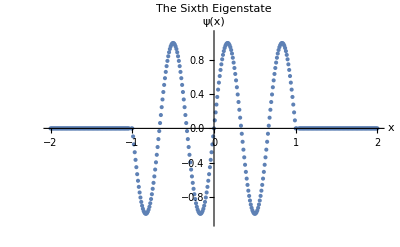

```mathematica
(*Exact Energies: hbar=m=1*)
Ev=N@(Pi^2/8)#^2&[{1,2,3,4,5,6}];
Print["First Six Energies(Exact): ",Ev] 
(*Shooting method eigenvalues*)
Print["First Six Energies(Numerical): ",Eval]
(*Shooting method eigenfunction*)
Table[ψ[[i]]=-ψ[[-i]],{i,pos0}];(*Getting the full wavefunction, odd one here->n=6*)
norm=2*dx*Sum[ψ[[i]]*ψ[[i]],{i,Round[Lx/4]+5,pos0}];(*Adding 5 steps to avoid divergent points at x=+1&-1*)
pairs=Table[{xL[[i]],ψ[[i]]/Sqrt[norm]},{i,Lx}];(*Getting ready to plot, and normalize*)
ListPlot[pairs,AxesLabel->{"x","ψ(x)"},PlotLabel->"The Sixth Eigenstate",PlotRange->{All,{-1.1,1.1}}]
```